the rules of chess occupy 10 to the 5 pages in this language.

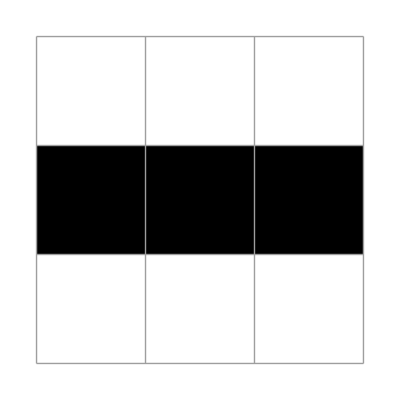
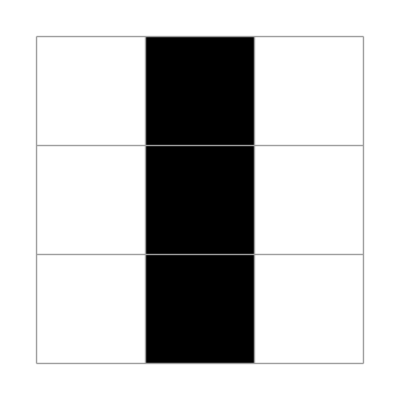

-Graphics-

```mathematica
X1=({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}});
plt/@NestList[updateLife[{3,3}][ #]&,
X1,1]
```

```mathematica
Binomial[8,7]
```

8

```mathematica
Not/@Prepend[{1,2,3,4} ,xP]
```

{!xP,!1,!2,!3,!4}

## the 8

```mathematica
lifeNeighbours={xNW,xN,xNE,xW,xE,xSW,xS,xSE};
lists8=(Prepend[#,Not[xP ]])&/@Subsets[lifeNeighbours,{7}];
the8=And@@Or@@@lists8
```

(!xP||xNW||xN||xNE||xW||xE||xSW||xS)&&(!xP||xNW||xN||xNE||xW||xE||xSW||xSE)&&(!xP||xNW||xN||xNE||xW||xE||xS||xSE)&&(!xP||xNW||xN||xNE||xW||xSW||xS||xSE)&&(!xP||xNW||xN||xNE||xE||xSW||xS||xSE)&&(!xP||xNW||xN||xW||xE||xSW||xS||xSE)&&(!xP||xNW||xNE||xW||xE||xSW||xS||xSE)&&(!xP||xN||xNE||xW||xE||xSW||xS||xSE)